```mathematica
Table[n=0;Boole[Not[PrimeQ[#]]]&/@(List@@(Times@@((x-#)&/@(Range[m]//Prime))//Expand)/.(x)->1),{m,200,300}]//ArrayPlot
```

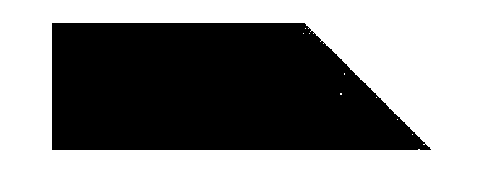

```mathematica
FractionalPart
```

```mathematica
{a,a,a,a,b,b,b,b,c,c,c,c}//.x1
```

{1,1,1,1,2,2,2,2,3,3,3,3}

```mathematica
x1={a->1,{x___,1,b,y___}->{x,1,2,y},{x___,2,b,y___}->{x,2,2,y},{x___,2,c,y___}->{x,2,3,y},{x___,3,c,y___}->{x,3,3,y}}
```

{a→1,{x___,1,b,y___}→{x,1,2,y},{x___,2,b,y___}→{x,2,2,y},{x___,2,c,y___}→{x,2,3,y},{x___,3,c,y___}→{x,3,3,y}}